Select the parameter (.prm) file of the desired chromatogram. It is assumed that the chromatography files are in the same directory as the parameter file.

```mathematica
SystemDialogInput["FileOpen" , {"C:/Users/fskdm/Dropbox", {"Parameter Files"->{"*.prm"}}}]
```

C:\Users\fskdm\My PhD\Projects\2019_12_20_PhD_Last_Project\2019_12_23_PAH_FAMEs\Chromatograms\RawData\2020_01_14-115152.dat.prm

```mathematica
pfile ="C:\\Users\\fskdm\\My PhD\\Projects\\2019_12_20_PhD_Last_Project\\2019_12_23_PAH_FAMEs\\Chromatograms\\RawData\\2020_01_14-115152.dat.prm"
```

C:\Users\fskdm\My PhD\Projects\2019_12_20_PhD_Last_Project\2019_12_23_PAH_FAMEs\Chromatograms\RawData\2020_01_14-115152.dat.prm

Extract the data directory:

```mathematica
filedir = FileNameJoin[ FileNameSplit[pfile][[1;;-2]]]
```

C:\Users\fskdm\My PhD\Projects\2019_12_20_PhD_Last_Project\2019_12_23_PAH_FAMEs\Chromatograms\RawData

Import the parameters:

```mathematica
params = Import[pfile, "Lines"]
```

{GC column description:	Rxi-5Sil MS 0.250 mm x 1 m,SFC flow rate:	0.800,SFC temperature:	22.000,GC flow rate: 	23.000,Experiment title: 	FAMES Canola,Sample name: 	Canola: Spar,Analysis type: 	Unknown,Concentration: 	9999.000,Operator name: 	DM,Detector sensitivity: 	1.0E-8,FID H2 flow rate: 	50.000,FID Air flow rate: 	300.000,SFC pressure: 	20265000 Pa,SFC dead time: 	30.000 s,File name: 	C:\SFC-GC\Data\2020_01_14-115152.dat,SFC gradient0:,Rate: 	0 $1 s^-1,Final:	0.000000 $1,Time:	5400.000 s,GC gradient0:,Rate: 	0 $1 s^-1,Final:	253.150000 $1,Time:	0.000 s,GC gradient1:,Rate: 	133 $1 s^-1,Final:	298.150000 $1,Time:	0.000 s,GC gradient2:,Rate: 	33 $1 s^-1,Final:	623.150000 $1,Time:	2.000 s,GC gradient3:,Rate: 	-200 $1 s^-1,Final:	593.150000 $1,Time:	0.000 s,GC idle temperature:	298.100000 Cdeg,GC purge temperature: 	473.150000 Cdeg,GC sampling temperature: 	253.150000 Cdeg,GC sampling time: 	10,GC load time: 	3,GC vent time: 	1}

```mathematica
file= FileNameJoin[
		{filedir
	,	FileNameSplit[
		StringSplit[                         
			params[[15]]                    (* Line 15 of the paramaters file contains the name of the data file *)
		][[3]]]                                        (* It is the third part of the line as separated by whitespace *)
		[[-1]]                                                 (* Select the last item on the list of the stringsplit *)
		}
	](* Extract the filename *)
```

C:\Users\fskdm\My PhD\Projects\2019_12_20_PhD_Last_Project\2019_12_23_PAH_FAMEs\Chromatograms\RawData\2020_01_14-115152.dat

```mathematica
FrontEndTokenExecute["SaveRename", {StringJoin[file,".nb"]}]
```

```mathematica
data=BinaryReadList[file, {"Integer8"}~Join~Table["Real64", {17}], ByteOrdering->-$ByteOrdering];
```

```mathematica
data[[1;;10]]//TableForm
```

0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1 | 29.997 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2 | 0.029 | 299.018 | 292.455 | 1.63979 | 0.960315 | 2.02151×10^7 | 144715. | 499.081 | 507.719 | 0.788849 | 239.804 | 0.670883 | 2.0265×10^7 | 2.76769×10^7 | 523.15 | 523.15 | 253.15
2 | 0.052 | 299.015 | 292.474 | 1.65274 | 0.965924 | 2.02154×10^7 | 144344. | 499.091 | 507.726 | 0.78902 | 239.804 | 0.671274 | 2.0265×10^7 | 2.76769×10^7 | 523.15 | 523.15 | 253.15
2 | 0.074 | 299.017 | 292.475 | 1.65372 | 0.966833 | 2.02172×10^7 | 144746. | 499.057 | 507.677 | 0.787836 | 239.804 | 0.670026 | 2.0265×10^7 | 2.76769×10^7 | 523.15 | 523.15 | 253.15
2 | 0.096 | 299.016 | 292.469 | 1.65376 | 0.9673 | 2.02194×10^7 | 144436. | 498.88 | 507.548 | 0.793954 | 239.804 | 0.675433 | 2.0265×10^7 | 2.76769×10^7 | 523.15 | 523.15 | 253.15
2 | 0.119 | 299.018 | 292.459 | 1.65407 | 0.966238 | 2.02199×10^7 | 142828. | 498.971 | 507.658 | 0.797223 | 239.804 | 0.678595 | 2.0265×10^7 | 2.76769×10^7 | 523.15 | 523.15 | 253.15
2 | 0.141 | 299.015 | 292.49 | 1.68085 | 0.982269 | 2.02174×10^7 | 141870. | 498.938 | 507.672 | 0.804037 | 239.804 | 0.684677 | 2.0265×10^7 | 2.76769×10^7 | 523.15 | 523.15 | 253.15
2 | 0.165 | 299.018 | 292.489 | 1.69213 | 0.986826 | 2.02194×10^7 | 142828. | 498.882 | 507.611 | 0.807776 | 239.804 | 0.688428 | 2.0265×10^7 | 2.76769×10^7 | 523.15 | 523.15 | 253.15
2 | 0.187 | 299.017 | 292.464 | 1.69344 | 0.98652 | 2.02189×10^7 | 142983. | 498.802 | 507.555 | 0.822046 | 239.804 | 0.701239 | 2.0265×10^7 | 2.76769×10^7 | 523.15 | 523.15 | 253.15

```mathematica
Length[data[[1]]]
```

18

```mathematica
data[[-5;;-1]]//TableForm
```

2 | 13.437 | 305.276 | 294.246 | 1.90566 | 1.90722 | 2.04489×10^7 | 174647. | 498.964 | 508.538 | 0.229791 | 571.627 | 0.148929 | 2.0265×10^7 | 2.76769×10^7 | 523.15 | 523.15 | 593.15
2 | 13.459 | 305.275 | 294.239 | 1.3354 | 1.39241 | 2.04464×10^7 | 174245. | 499.083 | 508.597 | 0.229221 | 611.185 | 0.149271 | 2.0265×10^7 | 2.76769×10^7 | 523.15 | 523.15 | 593.15
2 | 13.481 | 305.276 | 294.24 | 1.26789 | 1.34954 | 2.04471×10^7 | 173503. | 499.069 | 508.626 | 0.229276 | 631.978 | 0.14884 | 2.0265×10^7 | 2.76769×10^7 | 523.15 | 523.15 | 593.15
3 | 4202. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4 | 4202. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.

```mathematica
data[[-1]]
```

{4,4202.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
data[[1;;5]]//TableForm
```

0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1 | 29.997 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2 | 0.029 | 299.018 | 292.455 | 1.63979 | 0.960315 | 2.02151×10^7 | 144715. | 499.081 | 507.719 | 0.788849 | 239.804 | 0.670883 | 2.0265×10^7 | 2.76769×10^7 | 523.15 | 523.15 | 253.15
2 | 0.052 | 299.015 | 292.474 | 1.65274 | 0.965924 | 2.02154×10^7 | 144344. | 499.091 | 507.726 | 0.78902 | 239.804 | 0.671274 | 2.0265×10^7 | 2.76769×10^7 | 523.15 | 523.15 | 253.15
2 | 0.074 | 299.017 | 292.475 | 1.65372 | 0.966833 | 2.02172×10^7 | 144746. | 499.057 | 507.677 | 0.787836 | 239.804 | 0.670026 | 2.0265×10^7 | 2.76769×10^7 | 523.15 | 523.15 | 253.15

```mathematica
ListPlot[data[[All,12]]]
```

-Graphics-

```mathematica
values={"ID", "Time", "TAmbient", "Ttc", "Vb", "dV", "P1", "P2", "TInlet", "TOutlet", "Detector", "TColumn", "Vcol","P1 Setpoint", "P2 Setpoint", "TInlet Setpoint", "TOutlet Setpoint", "TColumn Setpoint"}
```

{ID,Time,TAmbient,Ttc,Vb,dV,P1,P2,TInlet,TOutlet,Detector,TColumn,Vcol,P1 Setpoint,P2 Setpoint,TInlet Setpoint,TOutlet Setpoint,TColumn Setpoint}

```mathematica
Join[{values}, {Range[18] } ]//TableForm
```

ID | Time | TAmbient | Ttc | Vb | dV | P1 | P2 | TInlet | TOutlet | Detector | TColumn | Vcol | P1 Setpoint | P2 Setpoint | TInlet Setpoint | TOutlet Setpoint | TColumn Setpoint
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18

Split the data by ID. Turns the list into a list of lists.

```mathematica
data2 = Split[data, #1[[1]]==#2[[1]]&];
```

```mathematica
Length[data]
```

239910

```mathematica
Length[data2]
```

1253

Find the times of the GC runs. This counts the number of GC runs, i.e. the length of the first dimension.

```mathematica
d1 = Select[data, #[[1]]==1&][[All, 2]];
```

```mathematica
d1
```

{29.997,39.997,49.997,59.997,69.997,80.097,90.097,100.197,110.197,120.197,130.297,140.297,150.297,160.297,170.297,180.297,189.897,199.797,209.797,219.797,229.797,239.797,249.797,259.797,269.797,279.797,289.797,299.797,309.797,319.797,329.797,339.797,349.797,359.797,369.797,379.797,389.797,399.797,409.797,419.797,429.797,439.797,449.797,459.797,469.797,479.697,489.697,499.797,509.797,519.797,529.797,539.797,549.797,559.797,569.797,579.797,589.797,599.797,609.797,619.797,629.797,639.797,649.797,659.797,669.797,679.897,689.997,699.997,709.997,719.997,729.997,739.997,749.997,759.997,769.997,780.097,790.097,800.097,810.097,820.097,830.097,840.197,850.197,860.197,870.197,880.197,890.197,900.297,910.297,920.297,930.297,940.297,950.297,960.297,970.297,980.397,990.397,1000.4,1010.4,1020.4,1030.4,1040.4,1050.4,1060.4,1070.4,1080.4,1090.4,1100.4,1110.4,1120.4,1130.4,1140.4,1150.4,1160.4,1170.4,1180.4,1190.4,1200.4,1210.4,1220.5,1230.5,1240.6,1250.6,1260.6,1270.6,1280.6,1290.7,1300.7,1310.7,1320.7,1330.7,1340.7,1350.8,1360.8,1370.8,1380.8,1390.8,1400.8,1410.8,1420.8,1430.8,1440.8,1450.9,1460.9,1470.9,1480.9,1491.,1501.,1511.,1521.,1531.,1541.1,1551.1,1561.1,1571.1,1581.1,1591.1,1601.1,1611.1,1621.1,1631.1,1641.1,1651.1,1661.1,1671.2,1681.2,1691.2,1701.2,1711.2,1721.2,1731.2,1741.2,1751.2,1761.2,1771.2,1781.2,1791.2,1801.2,1811.2,1821.2,1831.2,1841.3,1851.3,1861.4,1871.4,1881.4,1891.4,1901.4,1911.4,1921.4,1931.3,1941.4,1951.4,1961.4,1971.4,1981.5,1991.5,2001.5,2011.5,2021.6,2031.6,2041.6,2051.6,2061.6,2071.6,2081.6,2091.6,2101.5,2111.5,2121.5,2131.5,2141.5,2151.5,2161.5,2171.5,2181.5,2191.5,2201.5,2211.5,2221.5,2231.5,2241.5,2251.6,2261.6,2271.6,2281.6,2291.6,2301.6,2311.6,2321.7,2331.8,2341.8,2351.8,2361.8,2371.8,2381.8,2391.8,2401.8,2411.8,2421.8,2431.8,2441.8,2451.8,2461.8,2471.8,2481.8,2491.8,2501.8,2511.8,2521.8,2531.8,2541.8,2551.8,2561.9,2571.9,2581.9,2591.9,2601.9,2611.8,2621.8,2631.8,2641.8,2651.8,2661.8,2671.8,2681.8,2691.8,2701.8,2711.8,2721.9,2731.9,2741.9,2752.,2762.,2772.,2782.,2792.,2802.,2812.,2822.,2832.,2842.,2852.,2862.,2872.,2882.,2892.,2902.,2912.,2922.,2932.,2942.,2952.,2962.,2972.,2982.,2992.,3002.,3012.,3022.,3032.,3042.,3052.,3062.,3072.,3082.,3092.1,3102.1,3112.1,3122.1,3132.1,3142.1,3152.1,3162.1,3172.1,3182.1,3192.1,3202.1,3212.1,3222.2,3232.2,3242.2,3252.2,3262.2,3272.2,3282.2,3292.2,3302.2,3312.2,3322.2,3332.2,3342.2,3352.2,3362.2,3372.2,3382.2,3392.2,3402.2,3412.2,3422.2,3432.2,3442.2,3452.2,3462.2,3472.2,3482.2,3492.3,3502.3,3512.3,3522.3,3532.3,3542.3,3552.3,3562.3,3572.3,3582.4,3592.4,3602.4,3612.4,3622.4,3632.5,3642.5,3652.5,3662.6,3672.6,3682.6,3692.6,3702.6,3712.6,3722.6,3732.6,3742.6,3752.6,3762.6,3772.6,3782.6,3792.6,3802.6,3812.6,3822.6,3832.6,3842.7,3852.7,3862.7,3872.8,3882.8,3892.8,3902.9,3912.9,3922.9,3932.9,3942.9,3952.9,3962.9,3972.9,3983.,3993.,4003.,4013.,4023.,4033.,4043.,4053.,4063.,4073.,4083.,4093.,4103.,4113.1,4123.1,4133.1,4143.1,4153.1,4163.1,4171.9,4181.9,4191.9}

The number of GC runs:

```mathematica
Length[d1]
```

417

Check data integrity:
Number of GC runs (ID=2) + 2 per GC run (ID=1 and ID = 3) + ID=0 and ID=4

```mathematica
Length[d1]+Length[d1]*2 + 2
```

1253

Plot a GC run to see if looks sane:

```mathematica
Manipulate[
ListLinePlot[
	Select[data2, #[[1]][[1]] ==2& ][[gcrun]][[All,{2,dataset}]]
	, PlotLabel ->values[[dataset]]
]
	,{{gcrun,1,"GC Run"},1, Length[d1],1}
	,{{dataset,11, "Dataset"},1,18,1}
]
```

```mathematica
.
```

Delete wrong data:

First identify index of wrong data

```mathematica
Select[data2, #[[1]][[1]] ==2& ][[107]][[All,2]]
```

{0.033,0.056,0.079,0.114,0.137,0.159,0.182,0.207,0.23,0.252,0.274,0.297,0.319,0.341,0.365,0.387,0.409,0.448,0.471,0.494,0.516,0.538,0.561,0.583,0.622,0.645,0.667,0.69,0.714,0.737,0.759,0.782,0.821,0.845,0.867,0.889,0.923,0.946,0.968,0.991,1.032,1.054,1.078,1.118,1.141,1.163,1.186,1.215,1.238,1.261,1.283,1.317,1.34,1.363,1.385,1.407,1.441,1.463,1.485,1.525,1.548,1.571,1.593,1.616,1.638,1.661,1.683,1.705,1.745,1.767,1.789,1.819,1.842,1.864,1.888,1.91,1.932,1.955,1.977,1.999,2.025,2.047,2.069,2.091,2.113,2.136,2.158,2.18,2.202,2.242,2.265,2.287,2.309,2.332,2.355,2.377,2.399,2.422,2.444,2.466,2.488,2.511,2.534,2.557,2.579,2.619,2.641,2.664,2.686,2.718,2.74,2.763,2.785,2.809,2.831,2.854,2.875,2.898,2.92,2.942,2.964,2.987,3.009,3.032,3.055,3.078,3.119,3.142,3.165,3.187,3.215,3.24,3.263,3.285,3.323,3.349,3.371,3.393,3.432,3.455,3.478,3.5,3.534,3.556,3.578,3.618,3.64,3.663,3.686,3.711,3.734,3.757,3.779,3.817,3.84,3.863,3.885,3.913,3.936,3.958,3.981,4.017,4.04,4.063,4.085,4.117,4.14,4.162,4.184,4.21,4.234,4.257,4.279,4.301,4.341,4.364,4.386,4.411,4.439,4.461,4.483,4.515,4.538,4.56,4.583,4.613,4.636,4.658,4.68,4.712,4.734,4.757,4.779,4.813,4.836,4.86,4.882,4.911,4.933,4.955,4.978,5.,5.035,5.058,5.08,5.106,5.128,5.152,5.174,5.197,5.219,5.241,5.264,5.286,5.311,5.335,5.359,5.381,5.403,5.44,5.464,5.486,5.514,5.537,5.561,5.583,5.609,5.632,5.655,5.677,5.699,5.722,5.746,5.768,5.79,5.82,5.845,5.868,5.89,5.914,5.937,5.961,5.983,6.01,6.032,6.054,6.077,6.099,6.122,6.145,6.167,6.189,6.211,6.233,6.256,6.278,6.313,6.337,6.36,6.382,6.419,6.441,6.465,6.487,6.51,6.533,6.556,6.578,6.611,6.633,6.655,6.677,6.7,6.722,6.744,6.767,6.79,6.814,6.838,6.86,6.883,6.907,6.93,6.954,6.977,6.999,7.021,7.045,7.07,7.093,7.115,7.139,7.162,7.184,7.209,7.231,7.253,7.276,7.298,7.32,7.343,7.366,7.388,7.411,7.433,7.457,7.479,7.513,7.536,7.56,7.582,7.608,7.632,7.655,7.677,7.699,7.721,7.745,7.767,7.789,7.813,7.836,7.859,7.882,7.908,7.931,7.954,7.977,7.999,8.022,8.044,8.066,8.088,8.111,8.133,8.155,8.177,8.2,8.234,8.257,8.279,8.306,8.33,8.352,8.375,8.397,8.419,8.442,8.464,8.487,8.511,8.534,8.557,8.579,8.605,8.628,8.651,8.673,8.696,8.718,8.741,8.765,8.787,8.81,8.833,8.855,8.877,8.913,8.935,8.959,8.981,9.007,9.03,9.052,9.077,9.099,9.122,9.144,9.166,9.191,9.221,9.244,9.266,9.289,9.311,9.333,9.358,9.38,9.411,9.434,9.457,9.479,9.509,9.531,9.555,9.577,9.599,9.622,9.646,9.668,9.69,9.713,9.736,9.759,9.781,9.814,9.837,9.859,9.882,9.908,9.93,9.954,9.976,9.998,10.021,10.043,10.066,10.088,10.114,10.137,10.16,10.183,10.21,10.233,10.256,10.278,10.313,10.337,10.359,10.381,10.409,10.432,10.453,10.476,10.498,10.52,10.543,10.565,10.587,10.61,10.632,10.656,10.678,10.7,10.736,10.76,10.782,10.814,10.836,10.858,10.881,10.908,10.93,10.955,10.977,10.999,11.022,11.044,11.066,11.089,11.111,11.133,11.155,11.178,11.2,11.222,11.244,11.267,11.289,11.312,11.334,11.358,11.381,11.413,11.436,11.46,11.482,11.512,11.535,11.558,11.581,11.606,11.629,11.652,11.675,11.697,11.727,11.75,11.774,11.824,11.846,11.869,11.891,11.925,11.948,11.971,11.993,12.016,12.038,12.062,12.086,12.116,12.139,12.161,12.183,12.217,12.241,12.264,12.286,12.309,12.332,12.354,12.377,12.4,12.422,12.446,12.468,12.491,12.513,12.536,12.558,12.58,12.617,12.64,12.664,12.686,12.709,12.731,12.755,12.777,12.799,12.822,12.845,12.867,12.89,12.921,12.944,12.966,12.989}

Delete wrong data:

```mathematica
data2[[107*3+1+2]]=0
```

0

Check that data was deleted

```mathematica
data2[[109*3+1+2]][[-12;;-1]]
```

{{2,12.543,304.292,339.084,5.62898,6.11005,2.03211×10^7,-818256.,623.975,631.091,0.051535,629.374,-0.0122833,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.565,304.293,339.085,5.62948,6.1097,2.03214×10^7,-818565.,624.021,631.109,0.0514587,629.225,-0.012323,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.588,304.294,339.097,5.62956,6.11065,2.03207×10^7,-817978.,624.073,631.129,0.0513306,629.371,-0.0124054,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.61,304.293,339.077,5.63014,6.10977,2.03209×10^7,-817792.,624.078,631.125,0.0511719,629.117,-0.0124908,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.636,304.292,339.096,5.5837,6.05612,2.03232×10^7,-815319.,624.035,631.075,0.051297,628.567,-0.0121246,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.658,304.291,339.077,5.55763,6.03091,2.03235×10^7,-816463.,624.128,631.165,0.0512878,629.088,-0.0122833,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.681,304.291,339.077,5.55432,6.02879,2.03216×10^7,-816958.,624.1,631.165,0.0511505,629.339,-0.0126221,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.713,304.295,339.077,5.55583,6.0275,2.03211×10^7,-815350.,624.128,631.153,0.0510529,628.84,-0.012735,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.735,304.293,339.101,5.53895,6.01089,2.0324×10^7,-815195.,624.152,631.109,0.0510132,629.129,-0.0126862,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.758,304.293,339.094,5.53032,6.00199,2.03235×10^7,-815597.,624.228,631.211,0.0510376,629.21,-0.0126617,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.78,304.293,339.102,5.52975,6.00178,2.03237×10^7,-815319.,624.24,631.227,0.0511139,629.28,-0.0128387,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.81,304.292,339.11,5.53023,6.00126,2.03217×10^7,-815350.,624.219,631.232,0.0510315,629.102,-0.0127441,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15}}

```mathematica
Drop[data2, {42*3+1+2,
```

Examine data in relation with temperature:

```mathematica
Manipulate[
ListLinePlot[
Select[data2, #[[1]][[1]] ==2& ][[gcrun]][[All,{2,dataset}]]
, PlotLabel ->values[[dataset]]
,PlotRange->{0,10}
,AxesLabel->{"Time (s)"}
, Epilog->{Scale[
Point[
Select[data2, #[[1]][[1]] ==2& ][[gcrun]][[All,{2,12}]]
]
,{1,1/70.}
,{0,0}
]
}
](* Ends ListLine Plot*)
,{{gcrun,1,"GC Run"},1, Length[d1],1}
,{{dataset,11, "Dataset"},1,18,1}
] (* Ends Manipulate *)
```

Print an SFC time to see if it looks sane

```mathematica
d1[[1]]
```

29.997

Create 3D values {t_r1,t_r2,det}

```mathematica
Clear[f]
```

```mathematica
f[x_, y_]:= {Map[Prepend[#,x]&,y]}
```

The number of GC runs:

```mathematica
Select[data2, #[[1]][[1]] ==2& ][[All, All,{2,11}]]//Length
```

417

```mathematica
Length[d1]
```

417

```mathematica
data2d =Inner[f, d1, Select[data2, #[[1]][[1]] ==2& ][[All, All,{2,11}]], Join];
```

```mathematica
params //TableForm
```

GC column description:	Rxi-5Sil MS 0.250 mm x 1 m
SFC flow rate:	0.800
SFC temperature:	22.000
GC flow rate: 	23.000
Experiment title: 	FAMES Canola
Sample name: 	Canola: Spar
Analysis type: 	Unknown
Concentration: 	9999.000
Operator name: 	DM
Detector sensitivity: 	1.0E-8
FID H2 flow rate: 	50.000
FID Air flow rate: 	300.000
SFC pressure: 	20265000 Pa
SFC dead time: 	30.000 s
File name: 	C:\SFC-GC\Data\2020_01_14-115152.dat
SFC gradient0:
Rate: 	0 $1 s^-1
Final:	0.000000 $1
Time:	5400.000 s
GC gradient0:
Rate: 	0 $1 s^-1
Final:	253.150000 $1
Time:	0.000 s
GC gradient1:
Rate: 	133 $1 s^-1
Final:	298.150000 $1
Time:	0.000 s
GC gradient2:
Rate: 	33 $1 s^-1
Final:	623.150000 $1
Time:	2.000 s
GC gradient3:
Rate: 	-200 $1 s^-1
Final:	593.150000 $1
Time:	0.000 s
GC idle temperature:	298.100000 Cdeg
GC purge temperature: 	473.150000 Cdeg
GC sampling temperature: 	253.150000 Cdeg
GC sampling time: 	10
GC load time: 	3
GC vent time: 	1

```mathematica
plot3d = ListPlot3D[
Flatten[data2d,1]
,PlotRange->{All, All, All}
,AxesLabel->{"SFC (s)", "GC (s)","Detector (V)"}
,PlotLabel->StringSplit[params[[6]], ":"][[2]]
,Mesh -> None

(*, ColorFunction->"BlueGreenYellow"*)
]
```

-Graphics3D-

```mathematica
Show[plot3d, PlotRange->{All,All,{0,2}}]
```

-Graphics3D-

```mathematica
Show[plot3d, Graphics3D[{Red,Line[data2d]}], PlotRange->{All,All,{0,5}}]
```

-Graphics3D-

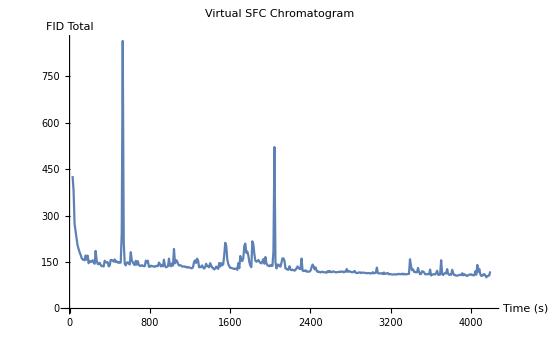

```mathematica
ListLinePlot[Partition[Riffle[d1,(Total[#]&/@data2d)[[All,3]]],2], PlotLabel->"Virtual SFC Chromatogram", AxesLabel->{"Time (s)","FID Total"}, PlotRange->All]
```

```mathematica
exportgraphic = Show[
	plot3d
	,PlotLabel -> Style["FAMEs: Canola oil", Large, Bold, Black]
	, AxesStyle -> {Directive[Black, Bold, 15]
				, Directive[Black, Bold, 15]
				, Directive[Black, Bold, 15]
				}
	,AxesLabel-> 
		{Style["SFC (s)", Large, Bold, Black]
		, Style[ "GC (s)",Large, Bold, Black]
		,Style[Rotate["Detector (V)", 90 Degree], Large, Bold, Black]
		}
	(*, ViewPoint->{10000,10000,10000} *)
	, ImageSize-> 1024
	, ViewPoint->vp
	
]
```

-Graphics3D-

```mathematica
Export["C:\\Users\\fskdm\\My PhD\\Conferences\\Analitika 2018\\Poster\\images\\Canola.png",exportgraphic,Background->None, ViewPoint->vp]
```

C:\Users\fskdm\My PhD\Conferences\Analitika 2018\Poster\images\Canola.png

```mathematica
Show[
	plot3d
(*	,Graphics3D[{Red,Line[data2d]}] *)
     , PlotLabel -> "Mystery Oil"
	, PlotRange-> {All, All,{0,0.1}}
]
```

```mathematica
ListContourPlot[Flatten[data2d,1], PlotRange->{All, All, All}, AxesLabel->{"SFC (s)", "GC (s)"}]
```

-Graphics-